# Split Drive Factorials

## 0) Functions

Plots

```mathematica
PlotLineDynamics[aggregatedGroupData_,genotypeIndex_,rgbaColors_,{opacity_,thickness_},plotRange_]:=ListLinePlot[
aggregatedGroupData[[All,All,genotypeIndex]]
,AspectRatio->1/3
,Frame->True
,FrameLabel->(Style[#,50]&/@{"Time","Allele Count"})
,FrameTicksStyle->20
,FrameStyle->Thick
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Thin]
,ImageSize->1500
,InterpolationOrder->1
,PlotRange->plotRange
,PlotRangePadding->0
,PlotStyle->Directive[rgbaColors[[genotypeIndex]],Thickness[thickness],Opacity[opacity]]
]
GenerateMatrixPlotsNonNormalized[aggregatedGroupData_,timeRange_,maxesMax_]:=Module[{matrixPlots,genotypeA},
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1/maxPopSize]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots
]
GenerateStreamChart[counts_]:=BarChart[counts//Transpose
,PerformanceGoal->"Speed"
,AspectRatio->1/4
,Axes->False
,FrameLabel->(Style[#,50]&/@{"Time","Genotype Breakdown"})
,BarSpacing->{0,0}
,ChartLayout->"Stacked"
,ChartStyle->(Directive[Opacity[.6],Lighter[#,0],EdgeForm[None]]&/@rgbColors)
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameTicks->{{None,Range[0,10000,100]},{Range[0,1.5*counts//Flatten//Max,250],None}}
,FrameTicksStyle->{
{Directive[Black,25],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,25]}
}
,GridLines->{Range[0,50000,100],Range[0,1.5*counts//Flatten//Max,100]}
,GridLinesStyle->Directive[Gray,Dashed]
,ImagePadding->Automatic
,ImageSize->2000
,PlotRangePadding->{0,0}
,PlotRange->{{timeRange[[1]],All},{0,1.1*Max[Total/@Transpose[counts]]}}
,Epilog->Flatten[{Thickness[.001],Dashed,(Line[{{#,0},{#,1.1*Max[Total/@Transpose[counts]]}}]&/@{releaseTimes[[1]]})}]
]
GenerateMatrixPlotsSplits[matrixPlots_]:=GraphicsGrid[Prepend[
Transpose[{Show[#,FrameTicks->None]&/@matrixPlots}],
{Show[matrixPlots,FrameTicks->None]}
]]
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateBlendSettingCMYK[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateMatrixPlots[aggregatedGroupData_,timeRange_,maxesMax_,rgbaColors_]:=Module[{matrixPlots,genotypeA},
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeA=genotypeA/maxesMax;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots
]
hexifyColor[color_RGBColor]:=StringJoin["#",IntegerString[Round[Level[color,1]*255],16,2]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
```

Data

```mathematica
AggregateByGenotype[rawDataTotal_,genotypesGroups_]:=Module[{aggregatedData,outputTotals,totals,transposedTotals},
outputTotals=Table[
aggregatedData=#[[All,genotypesGroups[[i,1]]]]&/@rawDataTotal;
totals=Map[Total,aggregatedData,{2}];
totals
,{i,1,genotypesGroups//Length}];
transposedTotals=Transpose/@Transpose[outputTotals];
transposedTotals
]

GetMaxPopulation[aggregatedGroupData_,genotypesGroups_,timeRange_]:=Module[{i,maxes,genotypeA,genotypeAtemp,maxesMax},
i=1;
maxes=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeAtemp=Max[#]&/@genotypeA
,{i,1,genotypesGroups//Length}];
maxesMax=Max/@Transpose[maxes];
maxesMax
]

FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_]:=Module[{plotRight,plotLeft},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameLabel->(Style[#,30]&/@plotLabels)
]
]
CalculateCounts[aggregatedGroupData_,genotypesGroups_]:=Module[{genotypeTemp,genotypeTotal},
Table[
genotypeTemp=aggregatedGroupData[[All,All,i]];
genotypeTotal=Total/@Transpose[genotypeTemp];
genotypeTotal
,{i,1,Length[genotypesGroups]}]
]
ImportExperimentRawData[experimentString_]:=Module[{experimentFolders,releaseTimes,rawDataExperiments,cellFolder,sweepID,filenames,rawData,rawDataTotal,genotypes,null,drive,releases,size,filenamesFemale,filenamesMale,rawDataMale,rawDataFemale,a,b,c,d,e,f},
experimentFolders=FileNames[experimentString<>"/0*",Directory[]];
releaseTimes={releasesStart,(1*releasesInterval)+releasesStart};
rawDataExperiments=Table[
cellFolder=experimentFolders[[i]];
sweepID={null,a,b,c,d,e,f}=ToExpression/@(StringSplit[StringSplit[experimentString,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_*","AF1_*"};(*CHANGE TO AF1*)
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
rawDataTotal
,{i,1,experimentFolders//Length}];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&;
{rawDataExperiments,genotypes}
]
ImportExperimentRawDataByNode[experimentString_,nodePattern_]:=Module[{experimentFolders,releaseTimes,rawDataExperiments,cellFolder,sweepID,filenames,rawData,rawDataTotal,genotypes,null,drive,releases,size,filenamesFemale,filenamesMale,rawDataMale,rawDataFemale,a,b,c,d,e,f},
experimentFolders=FileNames[experimentString<>"/0*",Directory[]];
releaseTimes={releasesStart,(1*releasesInterval)+releasesStart};
rawDataExperiments=Table[
cellFolder=experimentFolders[[i]];
sweepID={null,a,b,c,d,e,f}=ToExpression/@(StringSplit[StringSplit[experimentString,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Patch"<>nodePattern<>".csv","AF1_Aggregate_Patch"<>nodePattern<>".csv"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
rawDataTotal
,{i,1,experimentFolders//Length}];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&;
{rawDataExperiments,genotypes}
]
CalculateGenotypesGroups[genotypes_]:=Module[{alleles,splits,genotypesGroups},
alleles=Flatten[StringPartition[#,1]&/@genotypes]//DeleteDuplicates;
splits=StringPartition[#,1]&/@genotypes;
genotypesGroups={
Flatten/@(Table[ConstantArray[i,Count[splits[[i]],#]]&/@alleles,{i,1,splits//Length}]//Transpose),
alleles
}//Transpose
]
CalculateGenotypesGroupsOnLocus[genotypes_,locusRange_]:=Module[{alleles,splits,genotypesGroups},
alleles=Flatten[StringPartition[#,1]&/@genotypes]//DeleteDuplicates;
splits=(StringPartition[#,1][[locusRange[[1]];;locusRange[[2]]]])&/@genotypes;
genotypesGroups={
Flatten/@(Table[ConstantArray[i,Count[splits[[i]],#]]&/@alleles,{i,1,splits//Length}]//Transpose),
alleles
}//Transpose
]
```

## 1) Load Data

```mathematica
(*Set the path for the experiments*)
{USER,DRIVE}={3,1};
If[DRIVE==1,SetDirectory["/Volumes/Pusheen/xjego-khuq3/SplitDrive/Datasets/05/EqualHoming/SplitDrive/2018_11_27_GARBAGE"]]
If[DRIVE==2,SetDirectory["/Volumes/Pusheen/xjego-khuq3/SplitDrive/Datasets/05/EqualHoming/InundativeRelease/2018_11_27_GARBAGE"]]
If[DRIVE==3,SetDirectory["/Volumes/Pusheen/xjego-khuq3/SplitDrive/Datasets/05/EqualHoming/CRISPR/2018_11_27_GARBAGE"]]
(**)
If[DRIVE==1||DRIVE==2,
genotypesGroups={
{{02,05,05,06,07,12,15,15,16,17,22,25,25,26,27},"H"},
{{04,07,09,10,10,14,17,19,20,20,24,27,29,30,30},"B"},
{{03,06,08,08,09,13,16,18,18,19,23,26,28,28,29},"R"},
{{01,01,02,03,04,11,11,12,13,14,21,21,22,23,24},"W"},
{{11,12,13,14,15,16,17,18,19,20,21,21,22,22,23,23,24,24,25,25,26,26,27,27,28,28,29,29,30,30},"C"}
};
modifier=1;
{rs,releases,ri}={20,20,7};
ecoIndex=4;
]
If[DRIVE==3,
genotypesGroups={
{{02,05,05,06,07},"H"},
{{04,07,09,10,10},"B"},
{{03,06,08,08,09},"R"},
{{01,02,02,03,04},"W"}
};
modifier=1;
{rs,releases,ri}={20,1,7};
]
(*Define genotypes colors*)
originalColorsValues={
{0,100,70,0},
{50,0,50,0},
{60,100,0,0},
{10,100,0,0},
{30,20,0,0}
};
cmykColors=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues;
rgbColors=ColorConvert[#,"CMYK"->"RGB"]&/@cmykColors;
Transpose[{Append[rgbColors,RGBColor[0., 0.25, 0.75]],Append[genotypesGroups[[All,2]],"Total"]}]//Grid
```

/Volumes/Pusheen/xjego-khuq3/SplitDrive/Datasets/05/EqualHoming/SplitDrive/2018_11_27_GARBAGE

RGBColor[1., 0., 0.30000000000000004] | H
RGBColor[0.5, 1., 0.5] | B
RGBColor[0.4, 0., 1.] | R
RGBColor[0.9, 0., 1.] | W
RGBColor[0.7, 0.8, 1.] | C
RGBColor[0., 0.25, 0.75] | Total

## 2) Health Analysis

Single Run

/Volumes/Pusheen/xjego-khuq3/SplitDrive/Datasets/05/EqualHoming/CRISPR/2018_11_27_ANALYZED/E_03_01_080_080_25_10000

{ⅇ,3,1,80,80,25,10000}

194

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
WW | WH | WR | WB | HH | HR | HB | RR | RB | BB

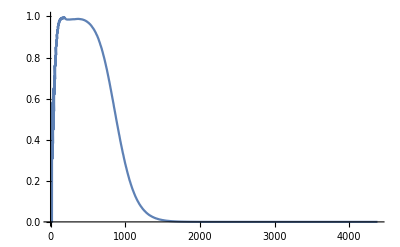

{1,80,25,522}

```mathematica
(**)
{patchString,threshold}={"0000",.8};
genotypesGroups={
{{5,6,7,12,15,16,17,22,25,26,27},"Hx"},
{{1,2,3,4,8,9,10,11,13,14,18,19,20,21,23,24,28,29,30},"Other"}
};
genotypesGroups={
{{2,5,6,7},"Hx"},
{{1,3,4,8,9,10},"Other"}
};
(*LoadExperiment*)
experimentFolders=folderPaths;
cellFolder=experimentFolders[[5]]
sweepID={null,drive,fitGRNA,femHoming,malHoming,releasesNum,mossyPerRelease}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last)
(*Releases*)
releasesEnd=startRelease+(releasesNum*releasesInterval)-1
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean_Patch"<>patchString<>".csv","AF1_Mean_Patch"<>patchString<>".csv"};
(*LoadData*)
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&
(*AggregateData*)
aggregatedGroupData=AggregateByGenotype[rawDataTotal,genotypesGroups][[1]];
(*Suppression*)
ratios=((#[[1]])/(#[[1]]+#[[2]]))&/@aggregatedGroupData;
ListLinePlot[ratios,PlotRange->{0,1}]

suppressionDays=Position[(threshold<#)&/@ratios,True]//Flatten;
suppressedAfterRelease=Cases[suppressionDays,a_/;a>releasesEnd];
bounceBack=If[Length[suppressedAfterRelease]>1,suppressedAfterRelease//Last,0];
suppressionTime=bounceBack-releasesEnd;
{fitGRNA,femHoming,releasesNum,suppressionTime}
```

MultiRun

```mathematica
factorials=Table[
(**)
{patchString,threshold}={"0000",.8};
genotypesGroups={
{{5,6,7,12,15,16,17,22,25,26,27},"Hx"},
{{1,2,3,4,8,9,10,11,13,14,18,19,20,21,23,24,28,29,30},"Other"}
};
genotypesGroups={
{{2,5,6,7},"Hx"},
{{1,3,4,8,9,10},"Other"}
};
(*LoadExperiment*)
experimentFolders=folderPaths;
cellFolder=experimentFolders[[i]];
sweepID={null,drive,fitGRNA,femHoming,malHoming,releasesNum,mossyPerRelease}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last);
(*Releases*)
releasesEnd=startRelease+(releasesNum*releasesInterval)-1;
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean_Patch"<>patchString<>".csv","AF1_Mean_Patch"<>patchString<>".csv"};
(*LoadData*)
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&;
(*AggregateData*)
aggregatedGroupData=AggregateByGenotype[rawDataTotal,genotypesGroups][[1]];
(*Suppression*)
ratios=((#[[1]])/(#[[1]]+#[[2]]))&/@aggregatedGroupData;
suppressionDays=Position[(threshold<#)&/@ratios,True]//Flatten;
suppressedAfterRelease=Cases[suppressionDays,a_/;a>releasesEnd];
bounceBack=If[Length[suppressedAfterRelease]>1,suppressedAfterRelease//Last,0];
suppressionTime=bounceBack-releasesEnd;
{fitGRNA,femHoming,releasesNum,If[suppressionTime>0,suppressionTime,0]}
,{i,1,Length[folderPaths]}];
Export["H_"<>experimentName<>"_factorials.csv",factorials]
```

CRISPR_factorials.csv

```mathematica
factorials=Import[experimentName<>"_factorials.csv"];
anchors=factorials[[All,3]]//DeleteDuplicates;
Table[
filtered=Cases[factorials,{a_,b_,i,c_}->{a,b,c}];
plot=ListDensityPlot[filtered
,ColorFunction->ColorData[{"DeepSeaColors",{0,factorials[[All,4]]//Max}}]
,ColorFunctionScaling->False
(*,FrameLabel->(Style[#,20]&/@{"gRNA Fitness","Homing"})*)
,FrameStyle->Thick
,FrameTicks->{{Automatic,None},{{{0,"0"},{2,"0.02"},{4,"0.04"},{6,"0.06"},{8,"0.08"},{10,"0.10"}},None}}
,FrameTicksStyle->Directive[35]
,GridLines->{Range[-1.5,11,1],Range[73,101,2]}
,GridLinesStyle->Directive[Thick,Opacity[.75],LightGray]
,ImagePadding->Automatic
,InterpolationOrder->0
,PlotRange->{{-.5,10.5},{73,101},All}
,PlotRangePadding->None
,PlotRangeClipping->False
];
Export[experimentName<>StringPadLeft[ToString[i],3,"0"]<>".pdf",plot,ImageSize->750]
,{i,anchors}]
bl=BarLegend[{"DeepSeaColors",{0,factorials[[All,4]]//Max}},50];
Export[experimentName<>"bar"<>".png",bl,ImageSize->750,ImageResolution->250]
```

{SplitDrive001.pdf,SplitDrive005.pdf,SplitDrive010.pdf,SplitDrive020.pdf,SplitDrive025.pdf}

SplitDrivebar.png

## 3) Ecological Analysis

Single Run

/Volumes/Pusheen/xjego-khuq3/SplitDrive/Datasets/05/EqualHoming/SplitDrive/2018_11_27_ANALYZED/E_01_01_080_080_25_10000

{ⅇ,1,1,80,80,25,10000}

194

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
WWWW | WWWH | WWWR | WWWB | WWHH | WWHR | WWHB | WWRR | WWRB | WWBB | WCWW | WCWH | WCWR | WCWB | WCHH | WCHR | WCHB | WCRR | WCRB | WCBB | CCWW | CCWH | CCWR | CCWB | CCHH | CCHR | CCHB | CCRR | CCRB | CCBB

Part::take: Cannot take positions 1 through 4 in 0.

Total::normal: Nonatomic expression expected at position 1 in Total[All].

Part::pkspec1: The expression Total[All] cannot be used as a part specification.

Part::take: Cannot take positions 1 through 4 in 0.

Total::normal: Nonatomic expression expected at position 1 in Total[All].

Part::pkspec1: The expression Total[All] cannot be used as a part specification.

Part::take: Cannot take positions 1 through 4 in 0.

General::stop: Further output of Part::take will be suppressed during this calculation.

Total::normal: Nonatomic expression expected at position 1 in Total[All].

General::stop: Further output of Total::normal will be suppressed during this calculation.

Part::pkspec1: The expression Total[All] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

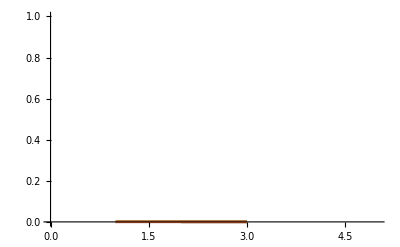

{1,80,25,-194}

```mathematica
(**)
{patchString,threshold}={"0000",.8};
(*LoadExperiment*)
experimentFolders=folderPaths;
cellFolder=experimentFolders[[5]]
sweepID={null,drive,fitGRNA,femHoming,malHoming,releasesNum,mossyPerRelease}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last)
(*Releases*)
releasesEnd=startRelease+(releasesNum*releasesInterval)-1
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean_Patch"<>patchString<>".csv","AF1_Mean_Patch"<>patchString<>".csv"};
(*LoadData*)
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&
(*AggregateData*)
aggregatedGroupData=AggregateByGenotype[rawDataTotal,genotypesGroups][[1]];
ratios=Table[
sampled=aggregatedGroupData[[i]];
normalizingTotals=Total/@sampled[[All,1;;4]];
sampled/normalizingTotals//N
,{i,1,aggregatedGroupData//Length}];
(*Suppression*)
ListLinePlot[ratios,PlotRange->{0,1}]

suppressionDays=Position[(threshold<#)&/@ratios,True]//Flatten;
suppressedAfterRelease=Cases[suppressionDays,a_/;a>releasesEnd];
bounceBack=If[Length[suppressedAfterRelease]>1,suppressedAfterRelease//Last,0];
suppressionTime=bounceBack-releasesEnd;
{fitGRNA,femHoming,releasesNum,suppressionTime}
```

```mathematica
sampled
```

{0.65,0.01,3860.66,16126.1,0}

MultiRun

```mathematica
factorials=Table[
(**)
{patchString,threshold}={"0000",.8};
(*LoadExperiment*)
experimentFolders=folderPaths;
cellFolder=experimentFolders[[i]];
sweepID={null,drive,fitGRNA,femHoming,malHoming,releasesNum,mossyPerRelease}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last);
(*Releases*)
releasesEnd=startRelease+(releasesNum*releasesInterval)-1;
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean_Patch"<>patchString<>".csv","AF1_Mean_Patch"<>patchString<>".csv"};
(*LoadData*)
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&;
(*AggregateData*)
aggregatedGroupData=AggregateByGenotype[rawDataTotal,genotypesGroups][[1]];
(*Suppression*)
ratios=((#[[4]])/(#[[1]]+#[[2]]+#[[3]]+#[[4]]))&/@aggregatedGroupData;
suppressionDays=Position[(threshold<#)&/@ratios,True]//Flatten;
suppressedAfterRelease=Cases[suppressionDays,a_/;a>releasesEnd];
bounceBack=If[Length[suppressedAfterRelease]>1,suppressedAfterRelease//Last,0];
suppressionTime=bounceBack-releasesEnd;
{fitGRNA,femHoming,releasesNum,If[suppressionTime>0,suppressionTime,0]}
,{i,1,Length[folderPaths]}];
Export["E_"<>experimentName<>"_factorials.csv",factorials]
```

E_SplitDrive_factorials.csv

```mathematica
factorials=Import["E_"<>experimentName<>"_factorials.csv"];
anchors=factorials[[All,3]]//DeleteDuplicates;
Table[
filtered=Cases[factorials,{a_,b_,i,c_}->{a,b,c}];
plot=ListDensityPlot[filtered
,ColorFunction->ColorData[{"DeepSeaColors",{0,factorials[[All,4]]//Max}}]
,ColorFunctionScaling->False
(*,FrameLabel->(Style[#,20]&/@{"gRNA Fitness","Homing"})*)
,FrameStyle->Thick
,FrameTicks->{{Automatic,None},{{{0,"0"},{2,"0.02"},{4,"0.04"},{6,"0.06"},{8,"0.08"},{10,"0.10"}},None}}
,FrameTicksStyle->Directive[35]
,GridLines->{Range[-1.5,11,1],Range[73,101,2]}
,GridLinesStyle->Directive[Thick,Opacity[.75],LightGray]
,ImagePadding->Automatic
,InterpolationOrder->0
,PlotRange->{{-.5,10.5},{73,101},All}
,PlotRangePadding->None
,PlotRangeClipping->False
];
Export[experimentName<>StringPadLeft[ToString[i],3,"0"]<>".pdf",plot,ImageSize->750]
,{i,anchors}]
bl=BarLegend[{"DeepSeaColors",{factorials[[All,4]]//Min,factorials[[All,4]]//Max}},50];
Export["E_"<>experimentName<>"bar"<>".png",bl,ImageSize->750,ImageResolution->250]
```

{SplitDrive001.pdf,SplitDrive005.pdf,SplitDrive010.pdf,SplitDrive020.pdf,SplitDrive025.pdf}

E_SplitDrivebar.png

```mathematica
Cases[factorials,{a_,b_,25,c_}->{a,b,c}]
```

{{1,80,3863},{1,82,3036},{1,84,2634},{1,86,2421},{1,88,2196},{1,90,2127},{1,92,2000},{1,94,1931},{1,96,1880},{1,98,1831},{2,80,2779},{2,82,2223},{2,84,1659},{2,86,1417},{2,88,1228},{2,90,1137},{2,92,1071},{2,94,1031},{2,96,994},{2,98,965},{3,80,1342},{3,82,1095},{3,84,870},{3,86,785},{3,88,745},{3,90,702},{3,92,685},{3,94,652},{3,96,643},{3,98,629},{4,80,603},{4,82,559},{4,84,544},{4,86,517},{4,88,504},{4,90,490},{4,92,475},{4,94,468},{4,96,456},{4,98,449},{5,80,406},{5,82,397},{5,84,388},{5,86,374},{5,88,367},{5,90,359},{5,92,356},{5,94,348},{5,96,342},{5,98,338},{6,80,289},{6,82,288},{6,84,280},{6,86,278},{6,88,274},{6,90,270},{6,92,267},{6,94,262},{6,96,260},{6,98,259},{7,80,207},{7,82,205},{7,84,202},{7,86,201},{7,88,200},{7,90,199},{7,92,197},{7,94,196},{7,96,194},{7,98,193},{8,80,144},{8,82,144},{8,84,143},{8,86,142},{8,88,142},{8,90,142},{8,92,140},{8,94,140},{8,96,140},{8,98,139},{9,80,98},{9,82,99},{9,84,98},{9,86,98},{9,88,97},{9,90,98},{9,92,98},{9,94,97},{9,96,97},{9,98,97},{10,80,65},{10,82,64},{10,84,65},{10,86,65},{10,88,66},{10,90,65},{10,92,65},{10,94,65},{10,96,65},{10,98,65}}

```mathematica
suppressionDays=Position[(threshold>#)&/@ratios,True]//Flatten
```

{20,21,22,27,28,29,34,35,36,41,42,43,48,49,50,55,56,57,58,62,63,64,65,69,70,71,72,76,77,78,79,80,83,84,85,86,87,90,91,92,93,94,97,98,99,100,101,102,104,105,106,107,108,109,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259}